# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## vMF (spherical Gaussian) Scattering

[Pomraning and Prinja 1995] - “Transverse Diffusion of a Collimated Particle Beam”
https://doi.org/10.1007/BF02178551

```mathematica
pVMF[u_,k_]:=k/(4Pi  Sinh[k])Exp[k u]
```

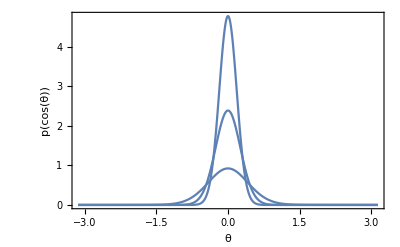

```mathematica
Show[
Plot[pVMF[Cos[t],5.8],{t,-Pi,Pi},PlotRange->All],
Plot[pVMF[Cos[t],15],{t,-Pi,Pi},PlotRange->All],
Plot[pVMF[Cos[t],30],{t,-Pi,Pi},PlotRange->All],

Frame->True,
FrameLabel->{{p[Cos[θ]],},{θ,"vMF, k = {5.8,15,30}"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pVMF[u,k],{u,-1,1},Assumptions->k>0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pVMF[u,k],{u,-1,1},Assumptions->k>0]
```

-1/k+Coth[k]

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->0,{u,-1,1},Assumptions->k>0]
```

1

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->1,{u,-1,1},Assumptions->k>0]
```

-3/k+3 Coth[k]

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->2,{u,-1,1},Assumptions->k>0]
```

(5 (3+k^2-3 k Coth[k]))/k^2

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->3,{u,-1,1},Assumptions->k>0]
```

(7 (-3 (5+2 k^2)+k (15+k^2) Coth[k]))/k^3

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->4,{u,-1,1},Assumptions->k>0]
```

(9 (105+45 k^2+k^4-5 k (21+2 k^2) Coth[k]))/k^4

### sampling

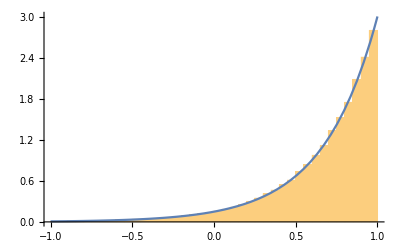

```mathematica
k=3;
Show[Histogram[Map[Log[E^-k(1-#)+E^k#]/k&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pVMF[u,k],{u,-1,1},PlotRange->All]

]
Clear[k];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pVMF[Log[E^-k(1-#)+E^k#]/k&[ξ],k],Assumptions->k>0&&0<ξ<1]
```

(k (-1+2 ξ+Coth[k]))/(4 π)